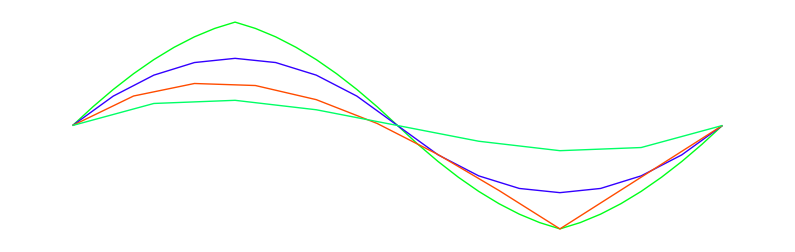

```mathematica
pts=Table[{Hue[0.35j],Table[{i,Sin[i]},{i,0,2 π, 1/6 j π}]},{j,1,4}];
Graphics[Table[{pts⟦i,1⟧,BezierCurve[pts⟦i,2⟧]},{i,1,4}]]
```